```mathematica
(*A=(Zd,S,N,f)*)
(*Zd: conj de vectores dimensión d sobre los num enteros*)
(*S: conj finito de estados*)
(*N: subconjunto finito de Zd- el vecindario de A*)
(*f: Sn+1->S  función de transición local de A*)

(*ACTIVIDAD*)

(*Diseñe un módulo Mathematica que tomando como entrada los siguientes parámetros nos proporcione como salida la simulación del AC unidimensional correspondiente:
	Inicial:Lista con la configuración inicial del AC
	Regla:Valor entero que codifica la regla como un número de Wolfram
	t:Número de configuraciones a calcular a partir de la configuración inicial

AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{},…]

Considere un conjunto de estados binario {0,1} y condición
de frontera periódica.Se recomienda implementar módulos para cada acción significativa de la simulación
(por ejemplo,un módulo que convierta el número de regla en una lista de listas,otro módulo que,a partir de una configuración calcule la siguiente,etc.)*)
```

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{regla,i ,listas,confAct},
regla = ACRegla[Regla];  (*regla en binario*)
listas = {};
confAct=Inicial;(*configuración actual*)
AppendTo[listas, confAct];  (*la primera configuración es la inicial*)
For [i=1,i≤t,i++,  (*todas las configuraciones*)
confAct=Config[confAct,regla]; (*calcular siguiente configuración*)
AppendTo[listas, confAct];
];
Return[ArrayPlot[listas]]; (*mostrar animación*)
];

(*módulo que convierte el número de regla en una lista de listas*)
ACRegla[Regla_Integer]:=Module[{res,b,i,elem},
res = {}; 
(*Calcular el binario de la regla*)
b=Reverse[IntegerDigits[Regla,2,8]];(*lista de longitud 8*)
(*Crear lista de 8 binarios, asignando b como su cuarto elemento*)
For[i=0,i<Length[b],i++,
elem=Reverse[IntegerDigits[i,2,3]];  (*crea tripletas binarias, del 0 al 7*)
elem = Append[elem,b[[i+1]]];  (*poner la cifra correspondiente*)
AppendTo[res,elem];
];
(*Print[res];*)
Return[res];
];

(*módulo que calcula la siguiente configuración*)
```

```mathematica
Config[Actual_List,Regla_List]:=Module[{res,res2,aux,i},
res = {};
aux={};  
(*se calcula usando la frontera periódica*)
For[i=1, i≤Length[Actual],i++,  (*recorres el estado actual*)
If[i==1, (*el primer elemento*)
aux={Actual[[Length[Actual]]],Actual[[i]],Actual[[i+1]],_}; 
(*vecino de la izquierda, actual, vecino derecha*)
,
If[i==Length[Actual], (*último elemento*)
aux={Actual[[i-1]],Actual[[i]],Actual[[1]],_};
, (*cualquier otro elemento*)
aux={Actual[[i-1]],Actual[[i]],Actual[[i+1]],_};
]; ];
res2 = Cases[Regla, aux]; (*hace matching y obtiene los estados de cada configuración*)
AppendTo[res,res2[[1,4]]]; (*el cuarto elemento de res2 es el resultado que debemos guardar*)
]; (*fin For*)
Return[res];
];
```

```mathematica
ACRegla[54];
```

{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0},{1,1,1,0}}

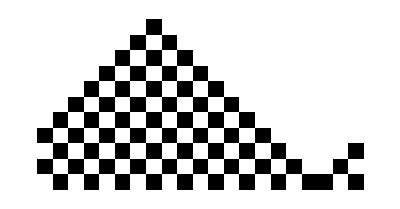

```mathematica
AC[{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},50,10]
```

```mathematica
Animacion[Inicial_List,Regla_Integer,t_Integer]:=Module[{lista,i,res,regla, aux, aux2},
lista={};
res = Inicial;
regla = ACRegla[Regla];  (*regla en binario*)
aux = {};
aux2 = {};
(*crear la secuencia en blanco, e ir metiendo las configuraciones según las obtenemos*)  
For[i=1,i≤Length[Inicial],i++,
AppendTo[aux,0];
];
For[i=1,i≤Length[Inicial],i++,
AppendTo[aux2,aux];
];
AppendTo[lista, ArrayPlot[aux2]];
For [i=1,i≤t,i++,  (*todas las configuraciones*)
aux2 = Rest[aux2];  (*quitas en primero*)
AppendTo[aux2, res]; (*añades el nuevo estado*)
res=Config[res,regla]; (*calcular siguiente configuración*)
AppendTo[lista, ArrayPlot[aux2]];
];
Return[ListAnimate[lista]];
];
```

```mathematica
Animacion[{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},50,20]
```